```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run"];
co={"../InputData/Coo100_1.txt","../InputData/Coo100m005_200.txt","../InputData/Coo100m005.txt"};
(*al1 22.4 1608662 /Max[tot[[365;;453,2]]]
al0 22.4 1608662 /Max[tot[[365;;453,2]]]*)
```

```mathematica
Do[
sfile={"../InputData/gamb_mortality_Jan25.csv","../InputData/arab_mortality_Jan25.csv","../InputData/fun_mortality_Jan25.csv"}[[sp]];
pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat={1,200,75736}[[i]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.5,eA=0.95,drivertime=270 365+150,NumDriver=1000,NumDriverPat={0,1,30}[[i]],d=0.005,Ld=10/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100,al0var=0.,al1=3700,amp=0,resp=1,recstart=365,recend=730,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=10sp+i,"e","r",start=28 365+1 ,co[[i]],"../InputData/RainDailyAvAv.csv","none",sfile}];
Export["PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,3},{sp,3}];
```

```mathematica
10585/365
```

29

```mathematica
10950/365
```

30

```mathematica
LinearSolve
```

```mathematica
out=Import["!./gdsimsapp<./PP"<>ToString[10 2+1]<>".csv","Table"];
```

```mathematica
totAll={{},{},{}};
Do[
out=Import["!./gdsimsapp<./PP"<>ToString[10 sp+1]<>".csv","Table"];
tot=Drop[Import["./output_files/Totals"<>ToString[10 sp+1]<>"run1.txt","Table"],2];
totW=N[tot[[366;;30 365,2]]];
totW/=Max[totW];
totAll[[sp]]=totW,{sp,3}];
```

```mathematica
(*Table[ListLinePlot[totAll[[i]]],{i,3}];
Dimensions[totAll]
Do[PrependTo[totAll[[i]],{"gam","arab","fun"}[[i]]],{i,3}];
Dimensions[totAll]
totAll=Transpose[totAll]
Export["Emerge29yr.csv",totAll];*)
```

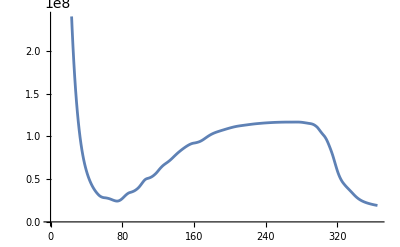

```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run/output_files"];
(*tot=Drop[Import["Totals4run1.txt","Table"],2];*)
tot=Drop[Import["Totals13run1.txt","Table"],2];
ListLinePlot[tot[[All,2]]]
```

```mathematica
MosPerHuman=18;
Dimensions[tot]
(*ListLogPlot[Table[tot[[366;;730,{1,i}]],{i,2,7,1}],PlotStyle->{Red,Blue,Green,Yellow,Orange,Purple},PlotRange->All,Joined->True]*)
Coo=Import["../../InputData/Coo100m005.txt","Table"];
Dimensions[Coo]
FracHouet=N[(Length[Coo]-Count[Coo[[All,5]],0])/Length[Coo]];
MaxHouet=FracHouet Max[tot[[100;;365,2]]];
(*NumMos = estimate of max num of mosquitoes - estimated mos per human * estimated num humans*)
NumMos=MosPerHuman 1608662;
correction=N[NumMos/MaxHouet]
```

{365,7}

{75736,7}

0.403815

```mathematica
25 365+150
```

9275

```mathematica
(29 365-25 365+150)/365.
```

4.41096

```mathematica
(* -------- Now set up gene drive runs ---------*)
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run"];
co={"../../InputData/Coo100m005.txt","../../InputData/Coo100m005_200.txt"};
dli={0.001,0.005,0.025};
xili={0.35,0.7};
Do[pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat={75736,200}[[yy]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xili[[xx]],eA=0.95,drivertime=25 365+150,NumDriver=50000,NumDriverPat={30,1}[[yy]],d=dli[[dd]],Ld=10/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100 correction,al0var=0.,al1=3700correction ,amp=0,resp=1,recstart=10,recend=maxT,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=10000(yy-1)+1000 xx+100dd+i-1,"e","r",start=23 365+1,co[[yy]],"../../InputData/RainDailyAvAv.csv","none","../../InputData/gamb_mortality_Jan25.csv"}];
Export["./RunBPars/PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,100},{xx,1},{dd,{2}},{yy,1}];
```

```mathematica
(* -------- Now set up gene drive runs ---------*)
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run"];
co={"../../InputData/Coo100m005.txt","../../InputData/Coo100m005_200.txt"};
dli={0.001,0.005,0.025};
xili={0.35,0.7};
Do[pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat={75736,200}[[yy]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xili[[xx]],eA=0.95,drivertime=25 365+150,NumDriver=0,NumDriverPat=0,d=dli[[dd]],Ld=10/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100 correction,al0var=0.,al1=3700correction ,amp=0,resp=1,recstart=10,recend=maxT,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=100000+10000(yy-1)+1000 xx+100dd+i-1,"e","r",start=23 365+1,co[[yy]],"../../InputData/RainDailyAvAv.csv","none","../../InputData/gamb_mortality_Jan25.csv"}];
Export["./RunAPars/PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,1},{xx,1},{dd,{2}},{yy,1}];
```

```mathematica
8396+3 365 +150
25 365+150
```

9641

9275

```mathematica
10000-8396
```

1604

```mathematica
1604/365.
```

4.39452

```mathematica
730+150
```

880

```mathematica
29 365
```

10585

```mathematica
23 365+1
29 365
```

8396

10585